# Equazione di Schrödinger

## Alcuni metodi semplici di soluzione:

## Shooting

Appunti Meccanica Quantistica
  G. Paffuti

#### Introduzione

Il problema agli autovalori "tipico" da risolvere per trovare gli autostati discreti dell'Hamiltoniana, in un sistema unidimensionale, è della forma

y''[x] + F[x] y[x] = λ y[x],

con condizioni al contorno omogenee

y[xL]=0;           y[xR]=0;

Un modo in teoria semplice per risolvere il problema è quello di trasformarlo in un usuale problema con condizioni iniziali e trovare per tentativi il valore di λ che soddisfa la condizione al bordo. L'idea base è mostrata in figura:

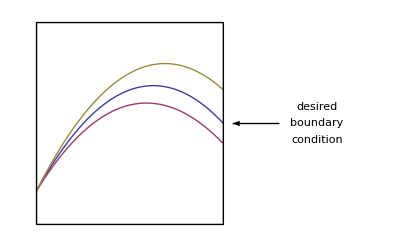

```mathematica
Plot[{-0.4x^2 + x,-0.4x^2+0.9x +0.01x^3,-0.4x^2+1.1x},{x,0,2},
PlotRange-> {{0,3.5},{-0.2,1}},
Axes-> False,Ticks->None ,Background-> White,
Epilog->{ Line[{{0,-0.2},{2,-0.2},{2,1},{0,1},{0,-0.2}}] ,
Text["desired",{3,0.5}],
Text["boundary",{3,0.4}],
Text["condition",{3,0.3}],
Arrow[{{2.6,0.4},{2.1,0.4}}]
}]
```

Si fanno dei tentativi di integrazione dell'equazione differenziale a partire da una condizione iniziale arbitraria in un estremo, l'errore sul valore della soluzione nell'altro estremo viene usato per modificare la condizione iniziale e così via in modo iterativo, finchè la soluzione trovata non converge alla soluzione del problema ai limiti.

Punto importante: l'equazione è lineare, questo permette di scegliere arbitrariamente la scala della funzione o della sua derivata in un punto (se ψ è una soluzione anche c ψ lo è ).

Uno dei vantaggi del metodo è quello di usare un integratore standard per le equazioni differenziali, NDSolve in Mathematica . Il lettore consulti l’help per avere informazioni sull’uso di questo comando.

#### Esempio

La funzione Sin[x] soddisfa all'equazione

y''+λ y  = 0 ;   con y[0]=y[π] = 0, per  λ=-1 (autovalore).

Risolviamo l'equazione per un arbitrario valore di λ con la condizione y[0]=0 e y'[0]=1: questo è possibile perchè l'equazione è lineare.

Scriviamo una funzione che ci fornisca, al variare di λ il valore della soluzione all'estremo x=π:

```mathematica
δ[λ_?NumberQ]:= ψ[π]/.First[NDSolve[{ψ''[x]+ λ ψ[x]== 0,ψ[0]== 0,ψ'[0]==1},ψ,{x,0,π}]]
```

A questo punto per trovare λ dobbiamo semplicemente trovare le radici di δ[λ]=0, cioè per quali valori di λ il valore al secondo estremo si annulla. Possiamo farlo usando FindRoot

```mathematica
λ/.FindRoot[δ[λ]==0,{λ,0.}]
```

1.

Se facciamo un disegno di δ[λ] riconosciamo facilmente le altre radici possibili,  1, 4,  9, etc.

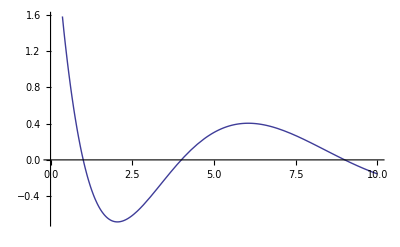

```mathematica
Plot[δ[λ],{λ,0,10}]
```

##### Mathematica nota

La sintassi

δ[λ_?NumberQ]

è dovuta al metodo in cui FindRoot valuta i suoi argomenti. Con questa sintassi la valutazione avviene solo se λ è un valore numerico, che è quanto voluto.

#### Meccanica Quantistica

La traduzione del metodo in Meccanica Quantistica è immediata, purchè nel caso di intervallo infinito si costruisca una "scatola" [x_L,x_R] (es. [-L,L] ) che contenga il sistema, o si effettui un cambiamento di variabili in modo fa ricondurre il sistema ad un intervallo finito. Per semplicità adotteremo la prima procedura.

Alcuni punti da tenere a mente per le applicazioni in Meccanica Quantistica

La regione in cui ψ è sensibilmente differente da zero di solito cresce con il numero quantico principale, quindi per stati eccitati L deve essere abbastanza grande.

Per L molto grandi si possono avere risultati senza senso perchè il valore della funzione è troppo piccolo e le variavioni al di sotto del parametro $MachinePrecision non sono catturate da Mathematica . Si può ovviare a questo problema aumentando la precisione, ma in questo caso il tempo di esecuzione aumenta.

È vivamente consigliato di controllare la stabilità dei risultati al variare del parametro L.

Se il potenziale è pari conviene usare una forma delle condizioni iniziali che sfruttino questa proprietà, tipicamente:

ψ pari :         ψ[0] = 1, ψ'[0] = 0

ψ dispari :     ψ[0] = 0, ψ'[0] = 1

### Discussione del metodo su un esempio

Consideriamo il solito oscillatore armonico, l’Hamiltoniana è

H = p^2/(2m)+ 1/2 m ω^2 x^2

Questo sistema è esattamente risolubile ed ha infiniti autovalori

E_n= ℏ ω (n + 1/2);   n=0,1,2,3,....

Nel seguito sceglieremo le unità di misura con ℏ = ω = m = 1 (unità naturali).

Il potenziale perciò si scrive:

```mathematica
V[x_]:= x^2/2;
```

Definiamo una scatola [-L,L] e riscriviamo la funzione δ definita sopra in modo da ammettere L come variabile, per poter effettuare dei controlli

```mathematica
δ[λ_?NumberQ,L_?NumberQ]:= ψ[L]/.First[NDSolve[{-1/2ψ''[x]+V[x] ψ[x]== λ ψ[x],ψ[-L]== 0,ψ'[-L]==1},ψ,{x,-L,L}]]
```

Per avere un' idea di come scegliere L, o si fa un ragionamento semiclassico oppure, almeno per lo stato fondamentale si nota che per grandi x la soluzione è del tipo Exp[-x^2/2] quindi per L=4 si ha già una soppressione Exp[-8].
In effetti

```mathematica
λ/.FindRoot[δ[λ,4.]==0,{λ,0.}]
```

0.5

In accordo con il valore dell' autovalore più basso.

Possiamo immediatamente constatare i Warning di Mathematica per L troppo grandi:

```mathematica
λ/.FindRoot[δ[λ,10.]==0,{λ,0.}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

0.5

Per evitare questi messaggi si può usare // Quiet. Un'alternativa è di sopprimere questi messaggi di default. I messaggi sono di tipo "lstol", come si vede dal messaggio precedente. Se si vogliono sopprimere i messaggi di questo tipo generati da FindRoot il comando è:

```mathematica
Off[FindRoot::"lstol"]
```

Se si vogliono ripristinare i messaggi si usi On[] al posto di Off[].

Possiamo controllare la variabilità in L usando il secondo argomento della funzione

```mathematica
values = Table[λ/.FindRoot[δ[λ,L]==0,{λ,0.}],{L,2,10,0.2}]
```

{0.537461,0.517663,0.507723,0.503112,0.501152,0.500391,0.500122,0.500035,0.500009,0.500002,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5}

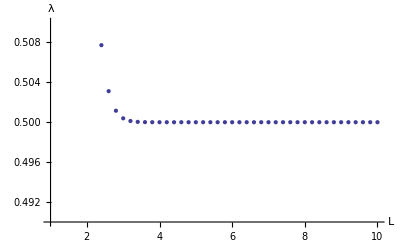

```mathematica
ListPlot[Transpose[{Range[2,10,0.2],values}],PlotRange->{{1,10},{0.49,0.51}},AxesOrigin->{1,0.49},AxesLabel-> {"L","λ"}]
```

Per studiare gli stati eccitati basta cambiare il punto di partenza della ricerca della radice in FindRoot. Ad esempio, con L=8

```mathematica
values = Table[λ/.FindRoot[δ[λ,8.]==0,{λ,start}],{start,0,3,0.2}]
```

{0.5,0.5,0.5,0.5,1.5,1.5,1.5,1.5,1.5,2.5,2.5,2.5,2.5,2.5,3.5,3.5}

Per eliminare i valori ripetuti si può, ad esempio, usare la funzione DeleteDuplicates

```mathematica
DeleteDuplicates[values,Abs[#1-#2]<10^-5&]
```

{0.5,1.5,2.5,3.5}

### Visualizzazione del processo

Può essere interessante seguire passo per passo i tentativi operati da FindRoot per trovare la soluzione, questo dà un'idea "dinamica" di cosa significa selezionare un autostato.

È possibile estrarre i valori intermedi trovati da FindRoot usando l'opzione EvaluationMonitor. Questa è da usare come una sostituzione posticipata, nella forma :> (
si scrive due punti >) perchè ovviamente la sostituzione non può essere effettuata prima di aver trovato la proposta di radice. EvaluationMonitor permette di manipolare il risultato intermedio, qui scegliamo semplicemente di appendere il risultato in fondo ad una lista. Alla fine si ha una lista di tutti i risultati intermedi

```mathematica
rList = {};rr=FindRoot[δ[λ,4.]==0,{λ,0.},EvaluationMonitor:>AppendTo[rList,λ]]
```

{λ→0.5}

Ecco i risultati intermedi , preceduti dal numero di tentativi

```mathematica
{Length[rList],rList}
```

{25,{0.,0.,1.49012×10^-8,0.186524,0.186524,0.186524,0.335154,0.335154,0.335154,0.437469,0.437469,0.437469,0.487883,0.487883,0.487883,0.499451,0.499451,0.499451,0.499999,0.499999,0.499999,0.5,0.5,0.500001,0.5}}

Possiamo usare questa lista per vedere come cambia la soluzione trovata da NDSolve al variare di λ:

```mathematica
Animate[Module[{L=4,V},
V[x_]:= x^2/2;
solution = NDSolve[{-1/2ψ''[x]+V[x] ψ[x]== λ  ψ[x],ψ[-L]== 0,ψ'[-L]==1},ψ,{x,-L,L}];
Plot[(ψ[x]/.solution)/(ψ[0]/.solution),{x,-L,L},PlotRange-> {{-L,L},{-1,2}}]],
{λ, rList},AnimationRunning->False,AnimationRepetitions-> 1]
```

## Raffinamenti del metodo

### Due vie

In alcuni casi può essere conveniente risolvere indipendentemente l'equazione a partire dai due estremi e porre la condizione di raccordo in un punto intermedio. Qui ad esempio scegliamo di confrontare le soluzioni imponendo la condizione di continuità per ψ'/ψ. Si faccia attenzione a NON usare 0 come punto intermedio per soluzioni dispari.
Il punto di raccordo è usato come terzo argomento della funzione (xM):

```mathematica
δ2Vie[λ_?NumberQ,L_?NumberQ, xM_,V_]:=  Module[{solLeft,solRight,ψ},
(solLeft =NDSolve[{-1/2ψ''[x]+V[x] ψ[x]== λ ψ[x],ψ[-L]== 0,ψ'[-L]==1},ψ,{x,-L,xM}][[1]];
solRight =NDSolve[{-1/2ψ''[x]+V[x] ψ[x]== λ ψ[x],ψ[L]== 0,ψ'[L]==-1},ψ,{x,L,xM}][[1]];
((ψ'[xM]/ψ[xM])/.solLeft) - ((ψ'[xM]/ψ[xM])/.solRight))]
```

Nell' esempio precedente

```mathematica
rList = {};rr=FindRoot[δ2Vie[λ,4.,0.,V]==0,{λ,0.},EvaluationMonitor:>AppendTo[rList,λ]];
```

```mathematica
{Length[rList],rList}
```

{16,{0.,0.,1.49012×10^-8,0.63662,0.63662,0.63662,0.513836,0.513836,0.513836,0.500134,0.500134,0.500134,0.500001,0.500001,0.500001,0.500001}}

Il risultato è stato trovato in meno passi (16 invece di 25) ma si sono risolte 2 equazioni per ogni passo.

Più in generale conviene tenere separati il limite sinistro ed il limite destro. Possiamo chiamare la funzione con lo stesso nome, differisce dalla precedente per il numero di argomenti:

```mathematica
δ2Vie[λ_?NumberQ,xL_?NumberQ,xR_?NumberQ, xM_,V_]:=  (solLeft =NDSolve[{-1/2ψ''[x]+V[x] ψ[x]== λ ψ[x],ψ[xL]== 0,ψ'[xL]==1},ψ,{x,xL,xM}][[1]];
solRight =NDSolve[{-1/2ψ''[x]+V[x] ψ[x]== λ ψ[x],ψ[xR]== 0,ψ'[xR]==-1},ψ,{x,xR,xM}][[1]];
((ψ'[xM]/ψ[xM])/.solLeft) - ((ψ'[xM]/ψ[xM])/.solRight))
```

### Pari e dispari

Come accennato precedentemente conviene usare direttamente le proprietà delle funzioni pari e dispari quando il potenziale è pari (e gli autostati possono quindi essere classificati secondo la loro parità). Le due funzioni seguenti sfuttano la forma delle condizioni iniziali indicate precedentemente:

ψ pari :            ψ[0] = 1, ψ'[0] = 0 
ψ dispari :     ψ[0] = 0, ψ'[0] = 1

Per generalità introduciamo anche il potenziale come variabile, in modo da poter usare queste funzioni in casi diversi:

```mathematica
δEven[λ_?NumberQ,L_?NumberQ, V_]:= ψ[L]/.(NDSolve[{-1/2ψ''[x]+V[x] ψ[x]== λ ψ[x],ψ[0]== 1,ψ'[0]==0},ψ,{x,0,L}][[1]]);
```

```mathematica
δOdd[λ_?NumberQ,L_?NumberQ, V_]:= ψ[L]/.(NDSolve[{-1/2ψ''[x]+V[x] ψ[x]== λ ψ[x],ψ[0]== 0,ψ'[0]==1},ψ,{x,0,L}][[1]])
```

Di nuovo come confronto:

```mathematica
V[x_]:= x^2/2;
```

```mathematica
rList = {};rr=FindRoot[δEven[λ,4.,V]==0,{λ,0.},EvaluationMonitor:>AppendTo[rList,λ]];
{Length[rList],rList}
```

{19,{0.,0.,1.49012×10^-8,0.288515,0.288515,0.288515,0.447804,0.447804,0.447804,0.49597,0.49597,0.49597,0.499974,0.499974,0.499974,0.5,0.5,0.5,0.5}}

Se si vuole migliorare la precisione del metodo occorre migliorare la precisione con cui opera NDSolve, con i parametri PrecisionGoal etc. (vedi help).

### Uso del metodo per trovare molti autovalori

I metodi precedenti permettono facilmente di trovare tutta una serie di autovalori, basta cambiare il punto di inizio in cui la funzione FindRoot cerca la soluzione. Gli eventuali doppioni possono essere eliminati dopo aver fatto il calcolo.

## Esempio: potenziale di Morse

Questo potenziale, per cui si risolve analiticamente l’equazione di Schrödinger, è usato come modello per descrivere le oscillazioni in molecole biatomiche. Il potenziale ha la forma

```mathematica
V[x_]:=  B (1-Exp[- x])^2;
```

Usiamo i risultati teorici noti (vedi ad esempio Landau 3) che forniscono i valori esatti degli autovalori. Sono quelli elencati nella formula seguente. Il valore di del parametro B è quello che compare nello studio della molecola di idrogeno. Nella molecola reale x rappresenta, in unità adimensionali, lo spostamento dal punto di equilibrio.

```mathematica
B = 151.294;
ω = √(2 B);
nMax = Floor[√(2*B)-0.5];
eneThH2=Table[ω (n+1/2) - 1/(4 B)ω^2 (n+1/2)^2,{n,0,nMax}]
```

{8.57253,24.9676,40.3626,54.7577,68.1528,80.5478,91.9429,102.338,111.733,120.128,127.523,133.918,139.313,143.708,147.103,149.498,150.893}

Abbiamo scelto il valore di B in modo che esistesse uno stato legato vicino alla soglia.

Un grafico che illustra il potenziale ed i livelli si può fare trovando l’intersezione della curva con l’energia degli stati:

```mathematica
pt=Table[{r/.FindRoot[V[r]== eneThH2[[k]],{r,-1.1,-5,-0.1}],
r/.FindRoot[V[r]== eneThH2[[k]],{r,6.5,0.1,10}]},{k,1,Length[eneThH2]}]
```

{{-0.213527,0.271857},{-0.340916,0.521272},{-0.416412,0.726725},{-0.471007,0.920312},{-0.513522,1.11221},{-0.54792,1.30805},{-0.576365,1.51212},{-0.60018,1.72848},{-0.620237,1.96162},{-0.637142,2.21704},{-0.651328,2.50209},{-0.663113,2.82726},{-0.672735,3.20866},{-0.68037,3.67333},{-0.686149,4.27251},{-0.690167,5.12404},{-0.692485,6.62659}}

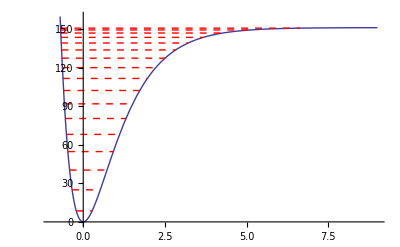

```mathematica
Plot[V[x],{x,-1,9},PlotRange-> {Automatic,{0,160}},
Epilog-> {Dashed, 
Red,Table[Line[{{pt[[k,1]],V[pt[[k,1]]]},
{pt[[k,2]],V[pt[[k,2]]]}}],{k,1,Length[pt]}]
}]
```

Come si vede dal grafico la zona -3, 7 ingloba ampiamente la parte rilevante della zona classicamente accessibile. La zona più delicata è quella vicina alla soglia, dove possono addensarsi (ed in effetti lo fanno) diversi autovalori, in questa zona l’intervallo di definizione della funzione và un pò allargato a destra, vista la forma del potenziale.

Facciamo quindi una spazzata con la funzione δ2Vie, creando due liste di autovalori

```mathematica
listaRoots1=Table[λ/.FindRoot[δ2Vie[λ,-3.,7.,0.,V]== 0,{λ,val}]//Quiet,
{val,0,0.95B,0.01 B}];
```

```mathematica
listaRoots2=Table[λ/.FindRoot[δ2Vie[λ,-3.5,20.,1.,V]== 0,{λ,val}]//Quiet,
{val,0.95B,B,0.002B}];
```

Per eliminare i duplicati eliminiamo i numeri che differiscono fra loro meno di 1/10000

```mathematica
eneShooting=DeleteDuplicates[Join[listaRoots1,Select[listaRoots2,(#<B)&]],
Abs[#1 - #2]< 10^-4 &]
```

{8.57253,24.9676,40.3626,54.7577,68.1528,80.5478,91.9429,102.338,111.733,120.128,127.523,133.918,139.313,143.708,147.103,149.498,150.893}

```mathematica
Length[eneShooting]
```

17

Abbiamo trovato 17 autovalori, come aspettato e la loro precisione è quella riportata nel grafico

```mathematica
maxdiff=Max[Abs[eneShooting-eneThH2]];
```

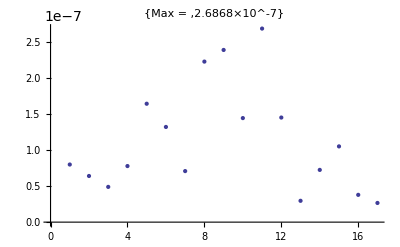

```mathematica
ListPlot[Abs[eneShooting-eneThH2],PlotLabel-> {"Max = ",maxdiff}]
```

Come si vede il metodo è preciso, anche se un pò inefficiente in questa formulazione. Il pericolo può essere di perdere qualche autovalore, un controllo si può fare usando il risultato dimostrato a lezione: il numero di autovalori è dato dal numero di zeri della soluzione ad energia nulla. In questo caso l’energia nulla (ionizzazione) corrisponde a E=B:

```mathematica
With[{xL=-4,xR = 20.},sol = ψ/.First[NDSolve[{-1/2ψ''[x]+V[x] ψ[x]== B ψ[x],ψ[0]== 1,ψ'[0]==1},ψ,{x,xL,xR}]]]
```

InterpolatingFunction[{{-4.,20.}},<>]

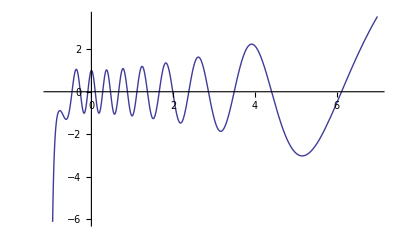

```mathematica
Plot[sol[x],{x,-1,7.}]
```

Ci sono effettivamente 17 zeri.

#### Confronto con la discretizzazione

Per confronto usiamo il programma per trovare gli autovalori esposto in EquazSchr-1.nb, modificando l’eggermente l’input in modo da accettare
limiti asimmetrici:

```mathematica
solveSch[V_,numEig_,{nP_,xL_,xR_}]:=
Module[{h,indDiag,D2,Ham,matV,ene,ψ,norm,xP,minV},
h = N[(xR - xL)/(nP+1)]; 
xP= xL + h* Range[nP];
D2 = SparseArray[{{i_,i_} ->  -2,{i_,j_}/;j-i==1-> 1,
{i_,j_}/; i-j== 1->  1},{nP,nP}];
indDiag = Table[{i,i},{i,1,nP}];
     matV = SparseArray[indDiag-> V[xP]];
minV = Min[V[xP]];
Ham =- 1/(2 h^2) D2 + matV;
{ene,ψ}=Eigensystem[Ham,numEig, Method-> {"Arnoldi","Shift"->( minV-0.01)}];
order = Ordering[ene];
ene = ene[[order]];
ψ = ψ[[order]]/Sqrt[h];
{xP,ene,ψ}]
```

```mathematica
{xP,ene,psi}=solveSch[V,17,{3000,-4.5,50}];
```

```mathematica
ene
```

{8.56953,24.9541,40.3311,54.7035,68.074,80.4447,91.8176,102.194,111.576,119.964,127.359,133.76,139.169,143.584,147.005,149.431,150.86}

Il massimo scostamento ora è

```mathematica
Max[Abs[ene-eneThH2]]
```

0.164518

come si vede molto più impreciso del metodo precedente, ma abbastanza rapido.